```mathematica
Exit[];
```

```mathematica
c={1-3 n^2 x^2+2 n^3 x^3,3 n^2 x^2-2 n^3 x^3,x-2 n x^2+n^2 x^3,-n x^2+n^2 x^3}
```

{1-3 n^2 x^2+2 n^3 x^3,3 n^2 x^2-2 n^3 x^3,x-2 n x^2+n^2 x^3,-n x^2+n^2 x^3}

```mathematica
b=1/n;
```

```mathematica
Y[i_,h_]:={y[i],y[i+1],m[i],m[i+1]}.c/.x->h;
{Y[i,0],Y[i,1/n],D[Y[i,x],x]/.x->0,D[Y[i,x],x]/.x->1/n}
```

{y[i],y[1+i],m[i],m[1+i]}

```mathematica
Simplify[(D[Y[1,x],{x,2}]/4 /n/.x->0)==0]
```

2 m[1]+m[2]+3 n y[1]==3 n y[2]

```mathematica
Simplify[(D[Y[n,x],{x,2}]/4 /n/.x->b)==0]
```

m[n]+2 m[1+n]+3 n y[n]==3 n y[1+n]

```mathematica
Simplify[(D[Y[i,x],{x,2}]/4 /n/.x->b)==(D[Y[i+1,x],{x,2}]/4 /n/.x->0)]
```

m[i]+4 m[1+i]+m[2+i]+3 n y[i]==3 n y[2+i]

```mathematica
M[n_]:=SparseArray[{{1,1}->-2,(n+1){1,1}->2,{n+1,n}->-2,{1,2}->2,{i_,j_}/;(i==j+1&&i<n+1&&i>1)->-1,{i_,j_}/;(i==j-1&&i<n+1&&i>1)->1},(n+1){1,1}];
M[5]//MatrixForm
```

(-2 | 2 | 0 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0 | 0
0 | -1 | 0 | 1 | 0 | 0
0 | 0 | -1 | 0 | 1 | 0
0 | 0 | 0 | -1 | 0 | 1
0 | 0 | 0 | 0 | -2 | 2)

# los:

```mathematica
y=Transpose[XY][[2]];y=Table[y[[i]],{i,1,Length[y],20}];If[y[[Length[y]]]≠XY[[Length[XY],2]],AppendTo[y,XY[[Length[XY],2]]]];n=Length[y]-1;m=M[n].y;
```

```mathematica
For[i=1,i≤n,i++,
delta=(y[[i+1]]-y[[i]])n;
If[delta==0,m[[i]]=0;m[[i+1]]=0,
a=m[[i]]/delta;b=m[[i+1]]/delta;
If[a^2+b^2>3,
t=3/Sqrt[a^2+b^2];m[[i]]=t a delta;m[[i+1]]=t b delta;]
]];
```

```mathematica
Y[x0_]:=Module[{i,x=x0,y=y,m=m,c=c,n=n},
i=Ceiling[x*n];
x-=(i-1)/n;
{y[[i]],y[[i+1]],m[[i]],m[[i+1]]}.{1-3 n^2 x^2+2 n^3 x^3,3 n^2 x^2-2 n^3 x^3,x-2 n x^2+n^2 x^3,-n x^2+n^2 x^3}
]
```

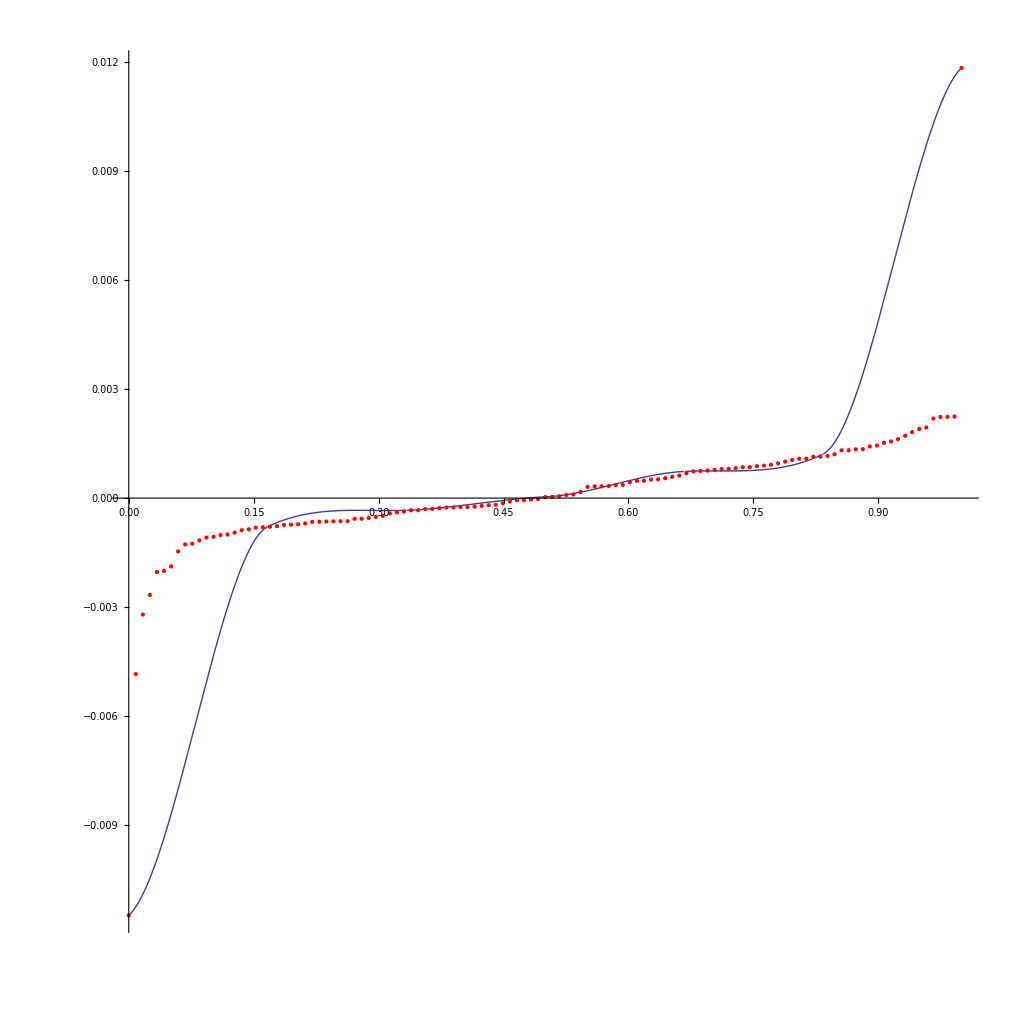

```mathematica
Show[Plot[Y[x],{x,0,1},AspectRatio->1,PlotRange->All],ListPlot[XY,PlotStyle->Red]]
```

```mathematica
<<Splines`
```

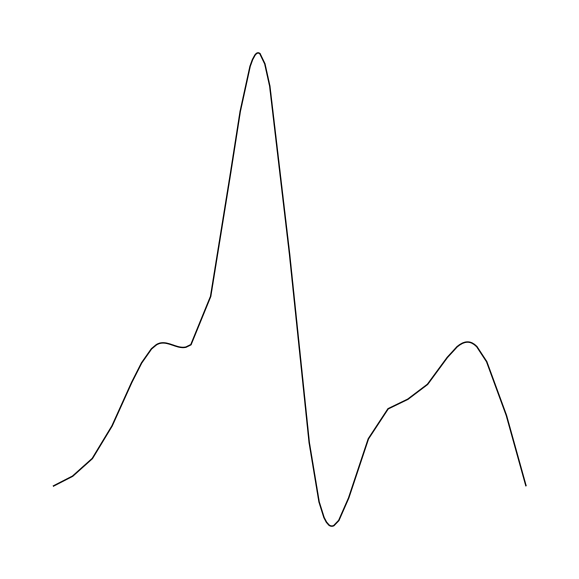

```mathematica
Graphics[Spline[Table[{i/(Length[y]-1),y[[i+1]]},{i,0,Length[y]-1}],Cubic],AspectRatio->1]
```

```mathematica
Y[x0_]:=Module[{i=n,x=x0,p=y,m=m,n=n,b,y},
If[x==0,i=1,
While[x≤(i-1)/n,i--];];
b=1/n;
{p[[i]],p[[i+1]],m[[i,1]],m[[i,2]],m[[n+i,1]],m[[n+i,2]]}.{1-(10 y^3)/b^3+(15 y^4)/b^4-(6 y^5)/b^5,(10 y^3)/b^3-(15 y^4)/b^4+(6 y^5)/b^5,y-(6 y^3)/b^2+(8 y^4)/b^3-(3 y^5)/b^4,-(4 y^3)/b^2+(7 y^4)/b^3-(3 y^5)/b^4,y^2/2-(3 y^3)/(2 b)+(3 y^4)/(2 b^2)-y^5/(2 b^3),y^3/(2 b)-y^4/b^2+y^5/(2 b^3)}/.y->(x-(i-1)/n)
]
```

```mathematica
y={XY[[1,2]],XY[[Length[XY],2]]};y=Transpose[XY][[2]];y=Table[y[[i]],{i,1,Length[y],2}];If[y[[Length[y]]]≠XY[[Length[XY],2]],AppendTo[y,XY[[Length[XY],2]]]];

n=Length[y]-1;
```

```mathematica
n
```

6

```mathematica
m=Table[ts[i,j],{i,2n},{j,2}];
```

```mathematica
d=(Y[#[[1]]]-#[[2]])^2&/@XY;d=Sum[d[[i]],{i,Length[d]}];g=Solve[Flatten[Table[D[d,ts[i,j]]==0,{i,2n},{j,2}]],Flatten[m]][[1]]
```

{ts[1,1]→1.0823,ts[1,2]→-3.6435×10^-6,ts[2,1]→-0.0151759,ts[2,2]→2.77363×10^-7,ts[3,1]→-0.0113918,ts[3,2]→2.8026×10^-6,ts[4,1]→0.0193723,ts[4,2]→0.,ts[5,1]→-0.0000660752,ts[5,2]→0.571534,ts[6,1]→-8.38091×10^-7,ts[6,2]→-0.00384619,ts[7,1]→1.11775×10^-6,ts[7,2]→1.0304×10^-6,ts[8,1]→0.00643999,ts[8,2]→-1.97915×10^-6,ts[9,1]→-0.0406935,ts[9,2]→1.06037×10^-6,ts[10,1]→-0.0002147,ts[10,2]→0.000164586,ts[11,1]→3.53879×10^-7,ts[11,2]→0.000792036,ts[12,1]→-2.59419×10^-11,ts[12,2]→5.14753×10^-7,ts[13,1]→4.53752×10^-7,ts[13,2]→0.0163343,ts[14,1]→-8.31444×10^-9,ts[14,2]→-1.03083×10^-7,ts[15,1]→7.14926×10^-9,ts[15,2]→-7.28265×10^-12,ts[16,1]→-0.00837183,ts[16,2]→-4.2512×10^-6,ts[17,1]→-0.00985838,ts[17,2]→-0.00375587,ts[18,1]→1.29474×10^-7,ts[18,2]→0.00153424,ts[19,1]→-3.59751×10^-7,ts[19,2]→-0.00155962,ts[20,1]→2.53477×10^-8,ts[20,2]→-3.25012×10^-8,ts[21,1]→-0.00814505,ts[21,2]→1.77568×10^-8,ts[22,1]→0.000612166,ts[22,2]→-3.55903×10^-7,ts[23,1]→0.144097,ts[23,2]→0.137109,ts[24,1]→-6.39497×10^-7,ts[24,2]→-0.00327646,ts[25,1]→2.66831×10^-7,ts[25,2]→9.11875×10^-6,ts[26,1]→-1.43491×10^-7,ts[26,2]→0.00194979,ts[27,1]→5.22883×10^-10,ts[27,2]→-3.14415×10^-8,ts[28,1]→-0.00253188,ts[28,2]→7.16435×10^-7,ts[29,1]→0.000761042,ts[29,2]→9.29119×10^-8,ts[30,1]→0.00727979,ts[30,2]→0.000626354,ts[31,1]→2.94519×10^-7,ts[31,2]→-0.00319948,ts[32,1]→-2.33249×10^-7,ts[32,2]→0.00946658,ts[33,1]→-1.37021×10^-7,ts[33,2]→1.83269×10^-7,ts[34,1]→-0.000435513,ts[34,2]→-6.99444×10^-9,ts[35,1]→0.000559624,ts[35,2]→1.99426×10^-7,ts[36,1]→0.00297729,ts[36,2]→5.79113×10^-7,ts[37,1]→-0.00305266,ts[37,2]→-0.00609373,ts[38,1]→5.1309×10^-7,ts[38,2]→0.00871657,ts[39,1]→2.00965×10^-8,ts[39,2]→-0.000350942,ts[40,1]→-1.82019×10^-8,ts[40,2]→1.45694×10^-8,ts[41,1]→0.000723568,ts[41,2]→4.64264×10^-8,ts[42,1]→-2.39426×10^-7,ts[42,2]→-4.05992×10^-11,ts[43,1]→-0.00494753,ts[43,2]→-0.00506425,ts[44,1]→1.46797×10^-7,ts[44,2]→-0.00465825,ts[45,1]→-8.14146×10^-8,ts[45,2]→-0.00227377,ts[46,1]→7.18358×10^-8,ts[46,2]→3.72287×10^-9,ts[47,1]→1.37114×10^-7,ts[47,2]→8.42229×10^-12,ts[48,1]→0.0125375,ts[48,2]→-6.35024×10^-7,ts[49,1]→-0.0272504,ts[49,2]→4.56494×10^-6,ts[50,1]→0.0373004,ts[50,2]→0.0249767,ts[51,1]→6.50168×10^-6,ts[51,2]→-0.071426,ts[52,1]→-4.84526×10^-7,ts[52,2]→0.00557458,ts[53,1]→-3.751×10^-7,ts[53,2]→-2.28261×10^-7,ts[54,1]→0.010349,ts[54,2]→2.39079×10^-7,ts[55,1]→-0.00449078,ts[55,2]→-1.97346×10^-7,ts[56,1]→0.000709043,ts[56,2]→-0.00386641,ts[57,1]→3.52967×10^-6,ts[57,2]→-0.0270599,ts[58,1]→-3.8275×10^-7,ts[58,2]→0.0196661,ts[59,1]→-0.00018142,ts[59,2]→6.67817,ts[60,1]→-34.345,ts[60,2]→-47.6272,ts[61,1]→-2.56596,ts[61,2]→1.82046,ts[62,1]→-16.,ts[62,2]→12.251,ts[63,1]→-18.8114,ts[63,2]→32.,ts[64,1]→339.047,ts[64,2]→-9.50602,ts[65,1]→7.0635,ts[65,2]→-3.09377,ts[66,1]→-26.3816,ts[66,2]→30.5071,ts[67,1]→12.2701,ts[67,2]→-17.964,ts[68,1]→15.8686,ts[68,2]→5.68961,ts[69,1]→0.084268,ts[69,2]→-0.306083,ts[70,1]→-1.49157,ts[70,2]→0.622097,ts[71,1]→0.000131837,ts[71,2]→0.000309723,ts[72,1]→-5.35569,ts[72,2]→12.5429,ts[73,1]→1.18473,ts[73,2]→-1.51892,ts[74,1]→-0.0000209261,ts[74,2]→-0.0000401053,ts[75,1]→16.9927,ts[75,2]→-19.296,ts[76,1]→1.0385,ts[76,2]→4.33681×10^-19,ts[77,1]→-0.6367,ts[77,2]→0.873711,ts[78,1]→2.8305,ts[78,2]→-0.185246,ts[79,1]→-0.495827,ts[79,2]→-1.28585,ts[80,1]→1.39899,ts[80,2]→0.175671,ts[81,1]→-0.366519,ts[81,2]→-2.,ts[82,1]→-0.487093,ts[82,2]→-1.96284,ts[83,1]→2.60241,ts[83,2]→-3.75542,ts[84,1]→-1.57432,ts[84,2]→1.13425,ts[85,1]→1.53906,ts[85,2]→0.502709,ts[86,1]→-0.0296981,ts[86,2]→-0.52828,ts[87,1]→-0.00306103,ts[87,2]→5.28408,ts[88,1]→-0.219279,ts[88,2]→0.438558,ts[89,1]→1.1985,ts[89,2]→0.,ts[90,1]→-1.39025,ts[90,2]→-2.61385,ts[91,1]→1.72055,ts[91,2]→-2.03868,ts[92,1]→2.32895,ts[92,2]→11.2633,ts[93,1]→-0.00243271,ts[93,2]→-0.0748942,ts[94,1]→1.38933,ts[94,2]→1.17664,ts[95,1]→-0.437468,ts[95,2]→2.3569,ts[96,1]→-1.7784,ts[96,2]→-3.35749,ts[97,1]→-2.88359,ts[97,2]→5.46428,ts[98,1]→-0.197677,ts[98,2]→0.214086,ts[99,1]→0.71371,ts[99,2]→0.28754,ts[100,1]→-0.346736,ts[100,2]→0.365231,ts[101,1]→0.0000959718,ts[101,2]→-0.000130176,ts[102,1]→-0.205296,ts[102,2]→-1.53448,ts[103,1]→-0.666426,ts[103,2]→-0.0768087,ts[104,1]→0.565089,ts[104,2]→-0.569554,ts[105,1]→-1.05936,ts[105,2]→-0.499442,ts[106,1]→-0.0011975,ts[106,2]→0.000174175,ts[107,1]→-0.000325132,ts[107,2]→-3.94381,ts[108,1]→2.52051,ts[108,2]→19.2403,ts[109,1]→-10.2788,ts[109,2]→-6.80745×10^-19,ts[110,1]→-34.8736,ts[110,2]→4.76171,ts[111,1]→4.3992,ts[111,2]→1.56344,ts[112,1]→11.2038,ts[112,2]→-5.41162,ts[113,1]→-4.,ts[113,2]→2.01487,ts[114,1]→0.319386,ts[114,2]→-1.01247,ts[115,1]→-0.6678,ts[115,2]→-1.02936,ts[116,1]→-15.4272,ts[116,2]→-22.929,ts[117,1]→2.50975,ts[117,2]→14.2177,ts[118,1]→2380.09,ts[118,2]→493.507}

```mathematica
m=Table[ts[i,j],{i,2n},{j,2}]/.g;
```

```mathematica
m[[1;;n]]=n/2 M[n].y;
```

```mathematica
m=Table[ts[i,j],{i,n},{j,2}]/.g;
For[i=1,i≤n,i++,
delta=(P[[i+1,2]]-P[[i,2]])/(P[[i+1,1]]-P[[i,1]]);
a=m[[i]]/delta;b=m[[i+1]]/delta;
If[a^2+b^2>3,
t=3/Sqrt[a^2+b^2];m[[i]]=t a delta;m[[i+1]]=t b delta;]
];m
```

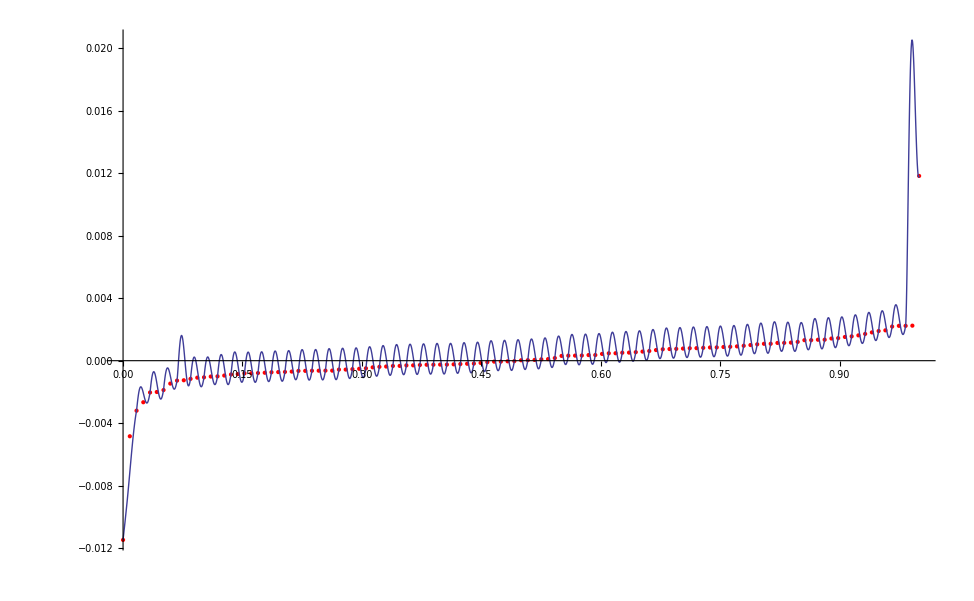

```mathematica
Show[ListPlot[{XY},PlotRange->All,PlotStyle->Red],Plot[Y[x],{x,0,1},PlotRange->All]]
```

```mathematica
Solve[Table[D[d,ys[i]]==0,{i,nN}],Table[ys[i],{i,nN}]]
```

{{ys[1]→-0.00547464,ys[2]→-0.000492335,ys[3]→-0.000911088,ys[4]→-0.00031071,ys[5]→-0.000185091,ys[6]→0.000265952,ys[7]→0.00060474,ys[8]→0.00113058,ys[9]→0.00100276,ys[10]→0.0046597}}

```mathematica
y=Table[ys[i],{i, nN}]/.%[[1]];
```

```mathematica
nN=10;y=Table[ys[i],{i, nN}];
```

0.000118941

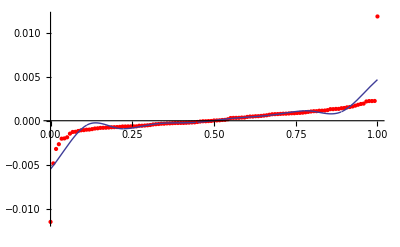

```mathematica
m=n/2M[n].y;n=Length[y]-1;d=(Y[#[[1]]]-#[[2]])^2&/@XY;d=Sum[d[[i]],{i,Length[d]}]
Show[ListPlot[XY,PlotStyle->Red,PlotRange->All],Plot[Y[x],{x,0,1},PlotRange->All]]
```

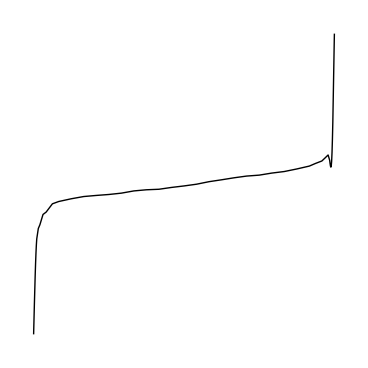

```mathematica
Graphics[Spline[XY,Cubic],AspectRatio->1]
```

```mathematica
Y[0]
```

0.01

```mathematica
{#[[1]]}&/@XY
```

{{0.},{0.008475},{0.016949},{0.025424},{0.033898},{0.042373},{0.050847},{0.059322},{0.067797},{0.076271},{0.084746},{0.09322},{0.101695},{0.110169},{0.118644},{0.127119},{0.135593},{0.144068},{0.152542},{0.161017},{0.169492},{0.177966},{0.186441},{0.194915},{0.20339},{0.211864},{0.220339},{0.228814},{0.237288},{0.245763},{0.254237},{0.262712},{0.271186},{0.279661},{0.288136},{0.29661},{0.305085},{0.313559},{0.322034},{0.330508},{0.338983},{0.347458},{0.355932},{0.364407},{0.372881},{0.381356},{0.389831},{0.398305},{0.40678},{0.415254},{0.423729},{0.432203},{0.440678},{0.449153},{0.457627},{0.466102},{0.474576},{0.483051},{0.491525},{0.5},{0.508475},{0.516949},{0.525424},{0.533898},{0.542373},{0.550847},{0.559322},{0.567797},{0.576271},{0.584746},{0.59322},{0.601695},{0.610169},{0.618644},{0.627119},{0.635593},{0.644068},{0.652542},{0.661017},{0.669492},{0.677966},{0.686441},{0.694915},{0.70339},{0.711864},{0.720339},{0.728814},{0.737288},{0.745763},{0.754237},{0.762712},{0.771186},{0.779661},{0.788136},{0.79661},{0.805085},{0.813559},{0.822034},{0.830508},{0.838983},{0.847458},{0.855932},{0.864407},{0.872881},{0.881356},{0.889831},{0.898305},{0.90678},{0.915254},{0.923729},{0.932203},{0.940678},{0.949153},{0.957627},{0.966102},{0.974576},{0.983051},{0.991525},{1.}}

```mathematica
Export["c:\\sdasd.txt",{Round[#[[1]]],#[[2]]}&/@(XY*(Length[XY]-1))]
```

c:\sdasd.txt